### Development Summary

I thought a Mathematica document might be more useful than a pdf. I think there are several reasons to be optimistic about the possibility of applying dispersion kernel techniques to Google’s Flu Trend Data. First and foremost is that google has increased the functionality of their API and doubled the spatial resolution (or at least the number of “advertising regions”). The concern about which search terms to use was taken care of by the addition of the “getTopQueries” method, which for a given query and set of restrictions (spatiotemporal) outputs the most highly correlated queries. Some of these are junk (“george bush” correlates to “Katrina,” but this probably isn’t helpful for finding μ), but others aren’t (“hurricane”, “katrina photos”, etc.). They also appear to have fixed whatever bug was limiting my access to a few hundred queries a day. The second is that google has added a visual interface to their trends API, making it very easy to find potentially interesting events/terms which can be used to extract a μ value. I believe this approach of using several different “events” which spread via the same medium (eg. different natural disaster searches all spread via news and word of mouth) will be useful in pulling the signal (μ of the medium) from the noise (event specific effects + generic randomness). The third is that mathematicas “geo-analysis” methods have become much more powerful. Finally, with several tweaks last semester, the kernel inversion procedure is working very consistently on two dimensional data for the full range of μ values considered, as well as for some non point source simulations (I use a fixed point method to calculate the pair μ,Τ where Τ is the “effective time” at which data collection begins). Hopefully this means it will be able to handle more realistic data like the flu which has no clear source. I’ve given several possible examples below.

Above is a rough picture of what I mean by “effective start time.” I’ll explain the method I’m using to find it geometrically tomorrow. I haven’t labelled my axes in the time series plots below; the vertical is search volume per day (order of one-ten million for the restricted regions and events below).

### Useful Preliminaries

```mathematica
dmas=Import["~/Desktop/BioPhys/flu_project/data_inputs/dmas.csv"][[2;;]];
dmas=Table[{dmas[[i]][[1]],dmas[[i]][[2]],dmas[[i]][[4]],dmas[[i]][[3]]},{i,1,Length[dmas]}];
dmadict=Table[dmas[[i]][[1]]->dmas[[i]],{i,1,Length[dmas]}];
latlongdict=Table[{dmas[[i]][[3]],dmas[[i]][[4]]}->dmas[[i]],{i,1,Length[dmas]}];
dmatoentry=Table[Transpose[#][[1]][[i]]->i,{i,1,Length[#]}]&;
```

```mathematica
geoball[dma_,radius_]:=
Return@Select[dmas,GeoDistance[GeoPosition[{(dma/.dmadict)[[3]],(dma/.dmadict)[[4]]}],GeoPosition[{#[[3]],#[[4]]}]]<radius Quantity[, "Miles"]&];
```

```mathematica
datetoindex[initialdate_,date_]:=
Return[1+DateDifference[initialdate,date][[1]]];

indextodate[initialdate_,index_]:=
Return[initialdate+Quantity[1, "Days"]*(index-1)];
```

```mathematica
uniformify[testdata_]:=(Transpose[testdata][[2]]/Max[Transpose[testdata][[2]]])[[1;;-1;;Floor[Length[testdata]/100.]]][[;;100]];
```

```mathematica
trainingset=ToExpression[#[[1]]]->ToExpression[#[[2]]]&/@Import["~/Desktop/BioPhys/flu_project/data_inputs/trainingset.csv"];
dataclassifier=Classify[trainingset];
```

trainingset={uniformify[#[[1]]],#[[2]]}&/@{bowlinggreenfludata[[1]][[2]]→True,bowlinggreenfludata[[2]][[2]]→True,bowlinggreenfludata[[3]][[2]]→False,bowlinggreenfludata[[4]][[2]]→True,bowlinggreenfludata[[5]][[2]]→True,bowlinggreenfludata[[6]][[2]]→True,bowlinggreenfludata[[12]][[2]]→False,bowlinggreenfludata[[7]][[2]]→False,bowlinggreenfludata[[18]][[2]]→False,bowlinggreenfludata[[19]][[2]]→True,greenvillefludata[[2]][[2]]→True,greenvillefludata[[1]][[2]]→False,greenvillefludata[[3]][[2]]→False,greenvillefludata[[4]][[2]]→False,greenvillefludata[[5]][[2]]→True,greenvillefludata[[6]][[2]]→True,baltimorefludata[[6]][[2]]→False};
Export["~/Desktop/BioPhys/flu_project/data_inputs/trainingset.csv",trainingset,"Data"];

```mathematica
τsimple[data_]:=Module[{zero,filtered},
(*Expects data in the form {{t(unitless), #hits},...}*)
filtered=Select[data,#[[2]]≠0&]; (*ignore points for which google has no data*)
zero=Sort[Transpose[filtered][[2]]][[Floor[Length[filtered]/5]]];
Return[Sum[#[[1]][[i]](#[[2]][[i]]-zero),{i,1,Length[#[[1]]]}]/(Total[#[[2]]]-Length[#[[2]]]*zero)&[Transpose[filtered]]];
];
```

```mathematica
counties=Flatten[AdministrativeDivisionData[#,"Subdivisions"]&/@Entity["Country","UnitedStates"]["AdministrativeDivisions"]];
```

```mathematica
fipstoshape=Table[counties[[i]]["FIPSCode"]->counties[[i]]["Polygon"],{i,1,Length[counties]}];
```

```mathematica
fipstopos=Table[counties[[i]]["FIPSCode"]->counties[[i]]["Position"],{i,1,Length[counties]}];
fipstoname=Table[counties[[i]]["FIPSCode"]->counties[[i]]["Name"],{i,1,Length[counties]}];
```

All data below is of the form {dma, latitude, longitude, timeseries}
The dmadict is of the form dma: {dma, location text, latitude, longitude}
dmatoentry is a lambda function whose output, given a dataset, is a function that gives the index of a dma in that dataset
geoball is a function that does what it sounds like; it gets all the data within a “radius” of a given dma.
datetoindex and indextodate go back and forth between using the # of days since initialdate and date objects as the independent variable

### CDC Data on the Flu, 1997-2015

Notes: Much lower spatial resolution than google, much more trustworthy.
Strategy: Integrate google data to course graining level of CDC, then try to match up the national picture as closely as possible. This will hopefully mean more trustworthy state level pictures.

Theory: To a good approximation, Ν_hits(r)/N_people=a+b r + c r^2. The meaning of the parameters is as follows: a is the mean number of searches due to “search noise” eg. the mean number of times a typical person would search for “flu” for reasons unrelated to having the virus, b is the approximate number of times a person with the virus will search for it, and c is the mean number of searches about the flu per conversation.

```mathematica
cdcdata=Import["~/Desktop/BioPhys/flu_project/data_inputs/FluViewPhase2Data/WHO_NREVSS_Combined_prior_to_2015_16.csv"];
Print[cdcdata[[1;;2]]];
cdcdata=cdcdata[[3;;]];
cdcdata = Select[cdcdata,#[[5]]≠"X"&&#[[6]]≠"X"&];
cdcstart=DateObject["dec-17-1997"];
```

{{*Beginning for the 2015-16 season, reports from public health and clinical laboratories are presented separately in the weekly influenza update, FluView.  This data file includes only data prior to the 2015-16 influenza season, and will be presented with the public health and clinical labs combined.},{REGION TYPE,REGION,YEAR,WEEK,TOTAL SPECIMENS,PERCENT POSITIVE,A (2009 H1N1),A (H1),A (H3),A (Subtyping not Performed),A (Unable to Subtype),B,H3N2v}}

```mathematica
Clear[dict]; Clear[keys];
```

```mathematica
dict[___]=-1;
keys={};
For[i=1,i<Length[cdcdata],i+=1,
date=DateString[DateObject["jan-01-"<>ToString[cdcdata[[i]][[3]]]]+cdcdata[[i]][[4]]Quantity[, "Weeks"]];
If[dict[date]==-1,
AppendTo[keys,date];
dict[date]=0.;,
dict[date]=dict[date]+cdcdata[[i]][[5]]*cdcdata[[i]][[6]]/100.
];
];
```

```mathematica
nationalcdcdata={DateObject[#],dict[#]}&/@keys;
maxnatcdc=Max[Transpose[nationalcdcdata][[2]]];
minnatcdc=Min[Transpose[nationalcdcdata][[2]]];
```

### “Flu” Search Data from 2005-2015 USA, 1day resolution.

Reasoning: Flu passes from person to person (local transmission) and causes google searches. 
Difficulties: Hard to isolate a source for a specific outbreak.
Top Correlated Searches: Avian Flu, Bird Flu, Flu Symptoms, Dog Flu, Flu Shots. Of these I would say only “flu symptoms” is useful.

```mathematica
fludata =Import["~/Desktop/BioPhys/flu_project/data_inputs/flu_data_2007-01-01_2015-01-01_day_2017-02-1002:34:35.910149.csv"][[2;;]];
For[i=1,i≤Length[fludata],i+=1,
fludata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[fludata[[i]][[4]],1],-1],","]];
];
flustart=DateObject["jan-01-2007"];
```

```mathematica
Manipulate[
t=Round[t];
Grid[{{indextodate[flustart,t]},{Show[GeoGraphics[GeoCircle[GeoPosition[{#[[3]],#[[4]]}]&[736/.dmadict],300 Quantity[, "Miles"]]],GeoRegionValuePlot[Table[GeoPosition[{fludata[[i]][[2]],fludata[[i]][[3]]}]->fludata[[i]][[4]][[t]],{i,1,Length[fludata]}],ColorFunction->ColorData["TemperatureMap"],
GeoLabels->(Tooltip[#1,#2[[1]]/.latlongdict ]&),GeoBackground->GeoStyling["ReliefMap"]
]]}}],Row[{Control[{t,1,Length[fludata[[1]][[4]]],1}],Spacer[5],"t is in days",Spacer[2]}]]
```

```mathematica
nationalfludata=Table[{indextodate[flustart,t],Total[Table[fludata[[i]][[4]][[t]],{i,1,Length[fludata]}]]},{t,1,Length[fludata[[2]][[4]]]}];
maxnat = Max[Transpose[nationalfludata][[2]]];
minnat=Min[Transpose[nationalfludata][[2]]];
```

```mathematica
maxnatr:=Max[√#&/@(Transpose[nationalfludata][[2]])];
maxnatl:=Max[Log[#+1]&/@(Transpose[nationalfludata][[2]])];
```

```mathematica
natfun=Interpolation[{datetoindex[flustart,#[[1]]],(#[[2]]-minnat)/(maxnat-minnat)}&/@nationalfludata[[1;;-1;;1]]];
cdcfun=Interpolation[{datetoindex[cdcstart,#[[1]]],(#[[2]])/(maxnatcdc)}&/@nationalcdcdata[[1;;-1;;1]]];
```

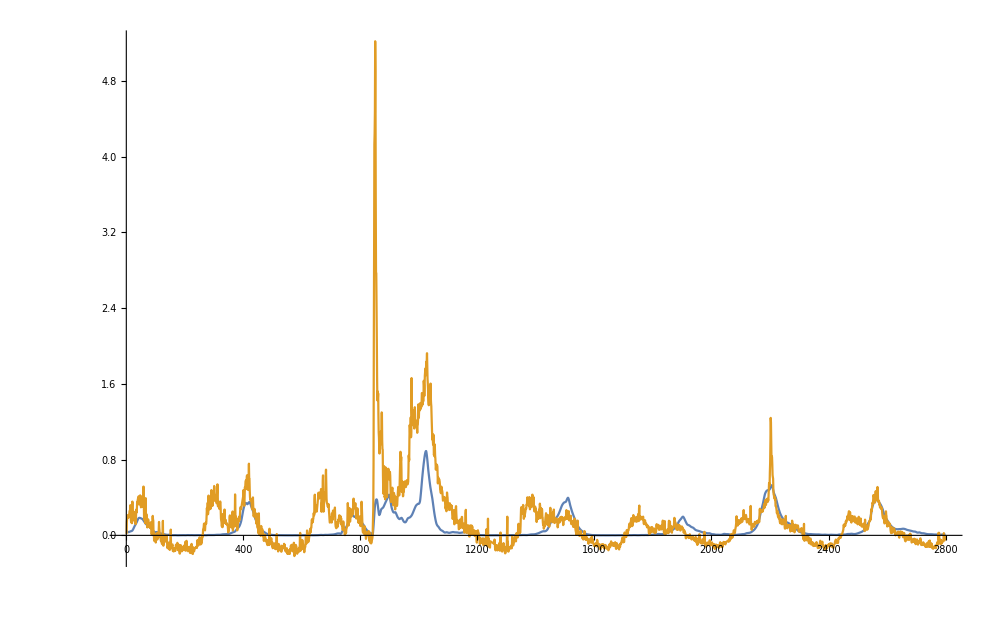

```mathematica
Plot[{cdcfun[x+3303],((-.15+√((.15)^2-4 .08(.015-#)))/(.08))&@natfun[x]},{x,1,2800},PlotRange->All]
```

```mathematica
f[α_]:=∑_(j=1)^2800 (cdcfun[j+3303]-natfun[j]^α)^2
```

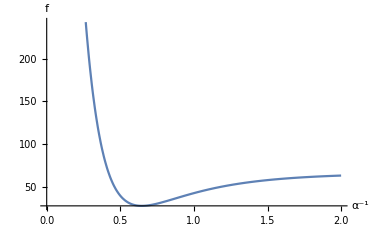

```mathematica
Plot[f[a],{a,0,2},AxesLabel->{"α^-1","f"}]
```

```mathematica
NMinimize[{f[a],0<a<2},a]
```

{28.3077,{a→0.645654}}

```mathematica
f2[a_,b_,c_]:=∑_(j=1)^2800 ((a#^2+b #+c)&[cdcfun[j+3303]]-natfun[j])^2
```

```mathematica
NMinimize[{f2[a,b,c],0<a<2,0<b<2,0<c<2},{a,b,c}]
```

{4.18085,{a→0.0799213,b→0.153546,c→0.0151314}}

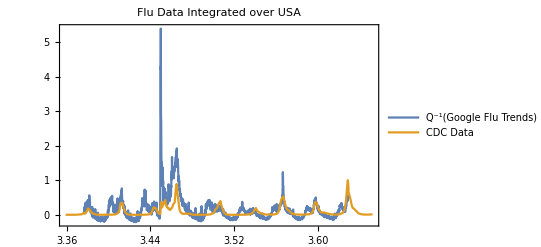

```mathematica
DateListPlot[{{#[[1]],((-.15+√((.15)^2-4 .08(.015-#)))/(.08))&[((#[[2]]-minnat)/(maxnat-minnat))]}&/@nationalfludata,{#[[1]],#[[2]]/maxnatcdc}&/@nationalcdcdata[[400;;]]},PlotRange->All,PlotLabel->"Flu Data Integrated over USA",PlotLegends->{"Q^-1(Google Flu Trends)","CDC Data"}]
```

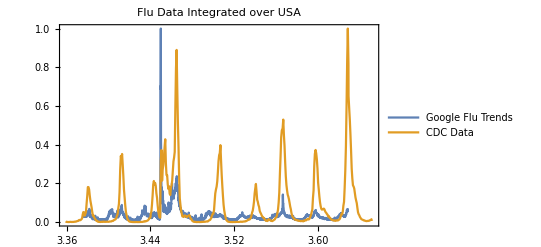

```mathematica
DateListPlot[{{#[[1]],(#[[2]]/maxnat)}&/@nationalfludata,{#[[1]],#[[2]]/maxnatcdc}&/@nationalcdcdata[[400;;]]},PlotRange->All,PlotLabel->"Flu Data Integrated over USA",PlotLegends->{"Google Flu Trends","CDC Data"}]
```

It is very interesting to note that how susceptible “search hits” are to the exponential “viralness” phenomenon. Perhaps it would be worthwhile to see what happens when one “rescales” by the national average.

```mathematica
Manipulate[
start=Round[start];
end=Round[end];
Grid[{{Text[fludata[[entry]][[1]]/.dmadict]},{StringJoin[{DateString[indextodate[flustart,start]]," through ",DateString[indextodate[flustart,end]]}]},
{DateListPlot[Table[{indextodate[flustart,t],(fludata[[entry]][[4]][[t]])^(.65)},{t,start,end}],PlotRange->All]}}],{entry,1,Length[fludata],1},{{end,100,"end date"},50,Length[fludata[[2]][[4]]]},{{start,1,"start date"},1,Length[fludata[[2]][[4]]]-50}]
```

Promising entries:
Baltimore 2009: 1, 1205, 900
Baltimore 2012-2013: 1, 2400, 2000
Flint-Saginaw 2012-2013: 2, 2400, 2000
Bowling-green 2013-2014: 149, 2800, 2400

```mathematica
544/.dmatoentry[fludata]
```

33

```mathematica
baltimoreball=geoball[545,300];
```

```mathematica
GeoRegionValuePlot[Table[GeoPosition[{baltimoreball[[i]][[3]],baltimoreball[[i]][[4]]}]->Mod[i,2],{i,1,Length[baltimoreball]}],GeoRange->"Country",ColorFunction->ColorData["DarkRainbow"],GeoLabels->(Tooltip[#1,#2[[1]]/.latlongdict]&),GeoBackground->GeoStyling["ReliefMap"]]
```

-Graphics-

```mathematica
baltimorefludata= Table[{Transpose[baltimoreball][[1]][[i]],Table[{DateObject["jan-01-2007"]+Quantity[1, "Days"]*(t-1),(fludata[[Transpose[baltimoreball][[1]][[i]]/.dmatoentry[fludata]]][[4]][[t]])^(.65)},{t,900,1205}]},{i,1,Length[baltimoreball]}];
rejectedbaltimore=Select[baltimorefludata,!dataclassifier[uniformify[#[[2]]]]&];
baltimorefludata=Select[baltimorefludata,dataclassifier[uniformify[#[[2]]]]&];
```

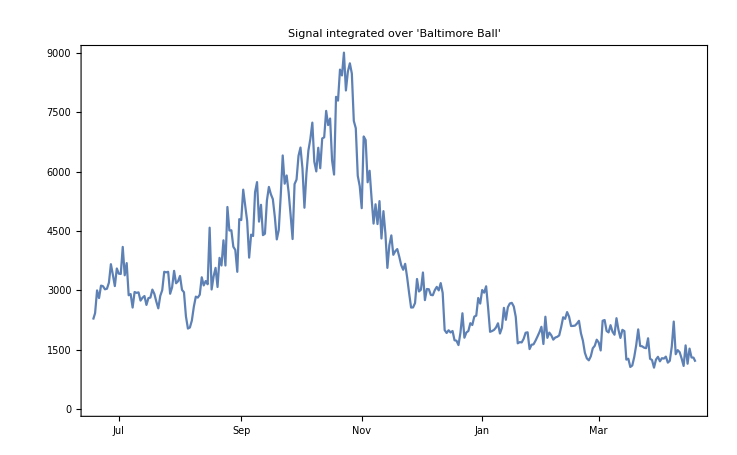

```mathematica
DateListPlot[Transpose[{Transpose[Transpose[baltimorefludata][[2;;]][[1]][[1]]][[1]],Total[#]&/@Transpose[(#[[2]]&/@#)&/@Transpose[baltimorefludata][[2;;]][[1]]]}],PlotRange->All, PlotLabel->"Signal integrated over 'Baltimore Ball'"]
```

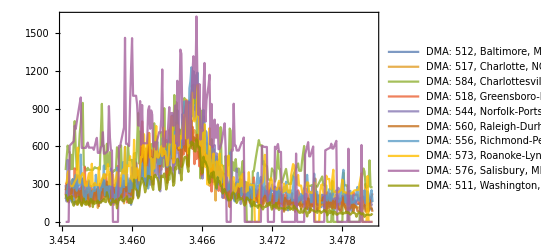

```mathematica
DateListPlot[
Transpose[baltimorefludata][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[baltimorefludata][[1]])]
```

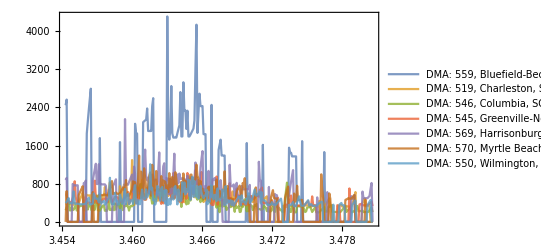

```mathematica
DateListPlot[
Transpose[rejectedbaltimore][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[rejectedbaltimore][[1]])]
```

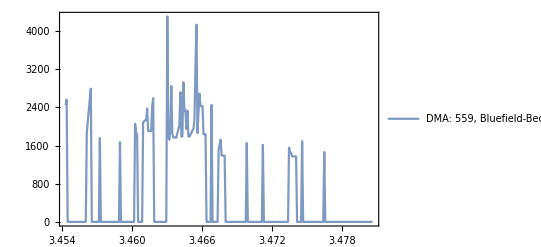

```mathematica
DateListPlot[
Transpose[rejectedbaltimore][[2]][[1]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[rejectedbaltimore][[1]])]
```

```mathematica
Manipulate[
i=Round[i];
testdata=baltimorefludata[[i]][[2]];
DateListPlot[
testdata
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->(("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]))&[baltimorefludata[[i]][[1]]]],
{i,1,Length[baltimorefludata],1}]
```

Using the τsimple method I have successfully assigned a reasonable “date” to the flu signal in Baltimore, MD. The next step is to apply this to every city in “baltimoreball” and see what kind of growth cone it spits out. Except perhaps for Harrisburg VA, entry four, which looks like garbage.

```mathematica
baltimorecone=Table[GeoPosition[Join[{#[[3]],#[[4]]}&[baltimorefludata[[i]][[1]]/.dmadict],{τsimple[Transpose[{datetoindex[flustart,#]&/@#[[1]],#[[2]]}&[Transpose[baltimorefludata[[i]][[2]]]]]]}]],{i,1,Length[baltimorefludata]}];
```

```mathematica
GeoRegionValuePlot[Table[baltimorecone[[i]]->Mod[i,2],{i,1,Length[baltimorecone]}],GeoLabels->(Tooltip[#1,ToString[#2[[1]][[;;2]]/.latlongdict]<>" occured at "<> ToString@#2[[1]][[3]]]&),ColorFunction->ColorData["DarkRainbow"],GeoBackground->GeoStyling["ReliefMap"]]
```

-Graphics-

```mathematica
ListPlot3D[Table[GeoGridPosition[baltimorecone[[i]],"Mercator"][[1]],{i,1,Length[baltimorecone]}],Mesh->All,PlotRange->All,AxesLabel->{"Latitude","Longitude","Time"}]
```

-Graphics3D-

Here the flow appears to be approximately north to south, but we are running into the problem of boundaries.

```mathematica
greenvilleball=geoball[545,400];
```

```mathematica
GeoRegionValuePlot[Table[GeoPosition[{greenvilleball[[i]][[3]],greenvilleball[[i]][[4]]}]->Mod[i,2],{i,1,Length[greenvilleball]}],GeoRange->"Country",ColorFunction->ColorData["DarkRainbow"],GeoLabels->(Tooltip[#1,#2[[1]]/.latlongdict]&),GeoBackground->GeoStyling["ReliefMap"]]
```

-Graphics-

```mathematica
greenvillefludata= Table[{Transpose[greenvilleball][[1]][[i]],Table[{DateObject["jan-01-2007"]+Quantity[1, "Days"]*(t-1),(fludata[[Transpose[greenvilleball][[1]][[i]]/.dmatoentry[fludata]]][[4]][[t]])^(.65)},{t,900,1205}]},{i,1,Length[greenvilleball]}];
rejectedgreenville=Select[greenvillefludata,!dataclassifier[uniformify[#[[2]]]]&];
greenvillefludata=Select[greenvillefludata,dataclassifier[uniformify[#[[2]]]]&];
```

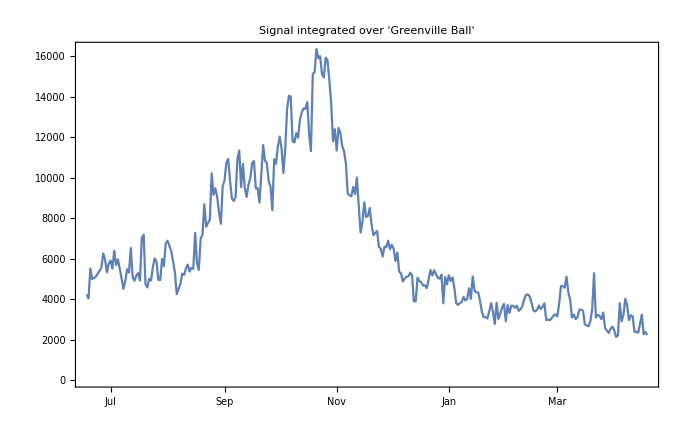

```mathematica
DateListPlot[Transpose[{Transpose[Transpose[greenvillefludata][[2;;]][[1]][[1]]][[1]],Total[#]&/@Transpose[(#[[2]]&/@#)&/@Transpose[greenvillefludata][[2;;]][[1]]]}],PlotRange->All, PlotLabel->"Signal integrated over 'Greenville Ball'"]
```

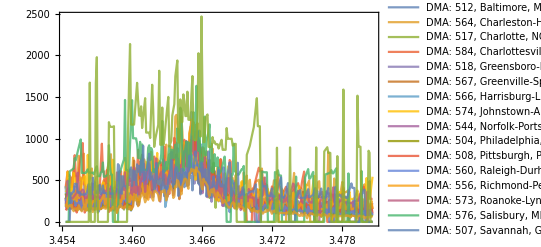

```mathematica
DateListPlot[
Transpose[greenvillefludata][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[greenvillefludata][[1]])]
```

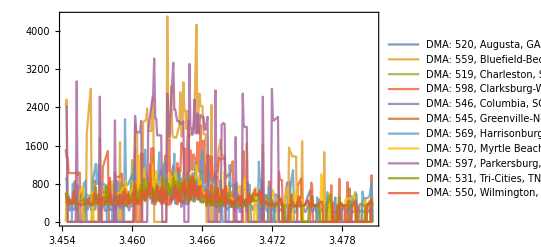

```mathematica
DateListPlot[
Transpose[rejectedgreenville][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[rejectedgreenville][[1]])]
```

```mathematica
Manipulate[
i=Round[i];
testdata=greenvillefludata[[i]][[2]];
DateListPlot[
testdata
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->(("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]))&[greenvillefludata[[i]][[1]]]],
{i,1,Length[greenvillefludata],1}]
```

```mathematica
greenvillecone=Table[GeoPosition[Join[{#[[3]],#[[4]]}&[greenvillefludata[[i]][[1]]/.dmadict],{τsimple[Transpose[{datetoindex[flustart,#]&/@#[[1]],#[[2]]}&[Transpose[greenvillefludata[[i]][[2]]]]]]}]],{i,1,Length[greenvillefludata]}];
```

```mathematica
GeoRegionValuePlot[Table[greenvillecone[[i]]->Mod[i,2],{i,1,Length[greenvillecone]}],GeoLabels->(Tooltip[#1,ToString[#2[[1]][[;;2]]/.latlongdict]<>" occured at "<> ToString@#2[[1]][[3]]]&),ColorFunction->ColorData["DarkRainbow"],GeoBackground->GeoStyling["ReliefMap"]]
```

-Graphics-

```mathematica
ListPlot3D[Table[GeoGridPosition[greenvillecone[[i]],"Mercator"][[1]],{i,1,Length[greenvillecone]}],Mesh->All,PlotRange->All,AxesLabel->{"Latitude","Longitude","Time"}]
```

-Graphics3D-

```mathematica
bowlinggreenball=geoball[736,300];
```

```mathematica
bowlinggreenfludata= Table[{Transpose[bowlinggreenball][[1]][[i]],Table[{DateObject["jan-01-2007"]+Quantity[1, "Days"]*(t-1),(fludata[[Transpose[bowlinggreenball][[1]][[i]]/.dmatoentry[fludata]]][[4]][[t]])^(.65)},{t,2400,2800}]},{i,1,Length[bowlinggreenball]}];
rejectedbowlinggreen=Select[bowlinggreenfludata,!dataclassifier[uniformify[#[[2]]]]&];
bowlinggreenfludata=Select[bowlinggreenfludata,dataclassifier[uniformify[#[[2]]]]&];
```

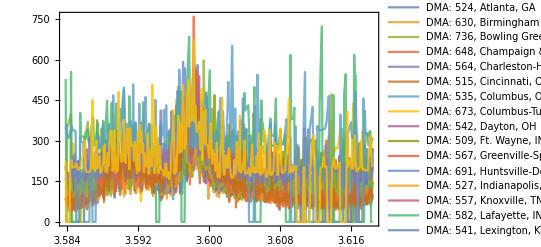

```mathematica
DateListPlot[
Transpose[bowlinggreenfludata][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[bowlinggreenfludata][[1]])]
```

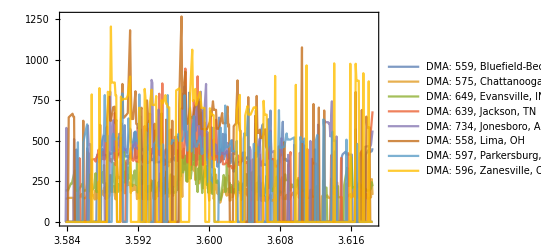

```mathematica
DateListPlot[
Transpose[rejectedbowlinggreen][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[rejectedbowlinggreen][[1]])]
```

```mathematica
dataclassifier[uniformify[bowlinggreenfludata[[3]][[2]]]]
```

True

```mathematica
Manipulate[
i=Round[i];
testdata=bowlinggreenfludata[[i]][[2]];
DateListPlot[
testdata
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->(("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]))&[bowlinggreenfludata[[i]][[1]]]],
{i,1,Length[bowlinggreenfludata],1}]
```

```mathematica
bowlinggreencone=Table[GeoPosition[Join[{#[[3]],#[[4]]}&[bowlinggreenfludata[[i]][[1]]/.dmadict],{τsimple[Transpose[{datetoindex[flustart,#]&/@#[[1]],#[[2]]}&[Transpose[bowlinggreenfludata[[i]][[2]]]]]]}]],{i,1,Length[bowlinggreenfludata]}];
```

```mathematica
GeoRegionValuePlot[Table[bowlinggreencone[[i]]->Mod[i,2],{i,1,Length[bowlinggreencone]}],GeoLabels->(Tooltip[#1,ToString[#2[[1]][[;;2]]/.latlongdict]<>" occured at "<> ToString@#2[[1]][[3]]]&),ColorFunction->ColorData["DarkRainbow"],GeoBackground->GeoStyling["ReliefMap"]]
```

-Graphics-

```mathematica
ListPlot3D[Table[GeoGridPosition[greenvillecone[[i]],"Mercator"][[1]],{i,1,Length[greenvillecone]}],Mesh->All,PlotRange->All,AxesLabel->{"Latitude","Longitude","Time"}]
```

-Graphics3D-

### “Katrina” Search Data from 8/01/2005 - 12/30/2005. Region within 600 miles of New Orleans.

Reasoning: Well specified event. News travels quickly but perhaps local news and the spread of “fear” and/or “concern” was somehow local (people talking to their friends, family, etc. Said fear/concern would produce google searches. 
Difficulties: Smaller amount of data since it is a single event. Unclear whether “spread of concern” is spatial (the internet is not spatial).
Top Correlated Searches: Hurricane, katrina hurricane, new orleans, hurricane katrina.

```mathematica
katrinadata=Import["~/Desktop/BioPhys/flu_project/data_inputs/katrina_data_2005-08-01_2005-12-30_day_2017-02-1003:16:18.232615.csv"][[2;;]];
For[i=1,i≤Length[katrinadata],i+=1,
katrinadata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[katrinadata[[i]][[4]],1],-1],","]];
];
katrinadata=Select[katrinadata,GeoDistance[GeoPosition[{#[[2]],#[[3]]}],GeoPosition[Entity["City",{"NewOrleans","Louisiana","UnitedStates"}]]]<600 Quantity[, "Miles"]&];
```

```mathematica
katrinadata[[5]][[1]]
```

530

```mathematica
Manipulate[
Grid[{{DateObject["aug-01-2005"]+Quantity[1, "Days"]*(t-1)},{
GeoRegionValuePlot[Table[GeoPosition[{katrinadata[[i]][[2]],katrinadata[[i]][[3]]}]->katrinadata[[i]][[4]][[t]],{i,2,Length[katrinadata]}],ColorFunction->ColorData["TemperatureMap"]]}}],Row[{Control[{t,1,Length[katrinadata[[4]][[4]]],1}],Spacer[5],"t is in days",Spacer[2]}]]
```

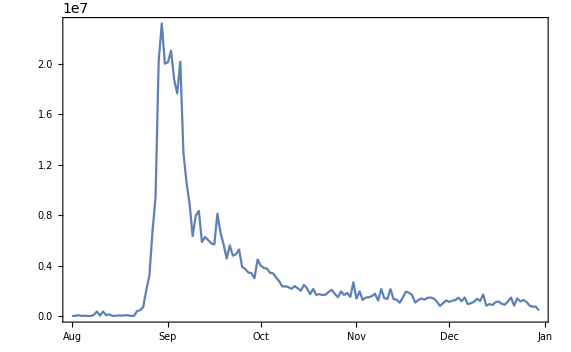

```mathematica
DateListPlot[Tooltip@Table[{DateObject["aug-01-2005"]+Quantity[1, "Days"]*(t-1),Total[Transpose[Table[{GeoPosition[{katrinadata[[i]][[2]],katrinadata[[i]][[3]]}],katrinadata[[i]][[4]][[t]]},{i,2,Length[katrinadata]}]][[2]]]},{t,1,Length[katrinadata[[2]][[4]]],1}],PlotRange->All]
```

This ramp up might be too fast for us to resolve spatially; it’s a shame that one wouldn’t expect “lack of concern” to spread like a disease, as it would be much easier to analyze.

### Cicada Search Data from 2/1/2004 - 7/1/2004 USA, 1 day resolution. Region within 1000 miles of DC.

Reasoning: Slower time ramp means it might be easier to resolve this data spatially. In both this case and the Katrina case, the rough geographic “ground zero” is known. Unclear whether this will provide a viable case for kernel extraction, as I think synchronized cicada emergence has more to do with ground temperatures than with some kind of signalling between them. Still, it’s an interesting test case. May 2004 was the largest Cicada resurgence in recent memory.
Difficulties: Synchronization might be forced externally via temperature rather than via local communication
Top Correlated Searches: Locust, Cicada Locust, Cicada Brood, Cicada Maryland

```mathematica
cicadadata=Import["~/Desktop/BioPhys/flu_project/data_inputs/cicada_data_2004-02-01_2004-07-01_day_2017-02-1003:30:06.393409.csv"];
For[i=2,i≤Length[cicadadata],i+=1,
cicadadata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[cicadadata[[i]][[4]],1],-1],","]];
];
```

```mathematica
cicadadata = Select[cicadadata[[2;;]],GeoDistance[GeoPosition[{#[[2]],#[[3]]}],GeoPosition[LinguisticAssistant]]<1000 LinguisticAssistant&];
```

```mathematica
Manipulate[
Grid[{{DateObject["feb-01-2004"]+Quantity[1, "Days"]*(t-1)},{
GeoRegionValuePlot[Table[GeoPosition[{cicadadata[[i]][[2]],cicadadata[[i]][[3]]}]->cicadadata[[i]][[4]][[t]],{i,2,Length[cicadadata]}],ColorFunction->ColorData["TemperatureMap"]]}}],Row[{Control[{t,1,Length[cicadadata[[4]][[4]]],1}],Spacer[5],"t is in days",Spacer[2]}]]
```

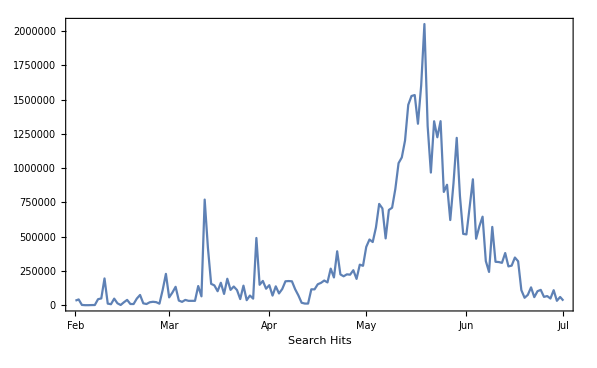

```mathematica
DateListPlot[Table[{DateObject["feb-01-2004"]+Quantity[1, "Days"]*(t-1),Total[Transpose[Table[{GeoPosition[{cicadadata[[i]][[2]],cicadadata[[i]][[3]]}],cicadadata[[i]][[4]][[t]]},{i,2,Length[cicadadata]}]][[2]]]},{t,1,Length[cicadadata[[2]][[4]]],1}],PlotRange->All,AxesLabel->{"Search Hits",None}]
```

```mathematica
cicadadata[[1]][[1]]
```

512

```mathematica
cicadadata2= Table[{Transpose[cicadadata][[1]][[i]],Table[{DateObject["feb-01-2004"]+Quantity[1, "Days"]*(t-1),cicadadata[[Transpose[cicadadata][[1]][[i]]/.dmatoentry[cicadadata]]][[4]][[t]]},{t,1,100}]},{i,1,Length[cicadadata]}];
```

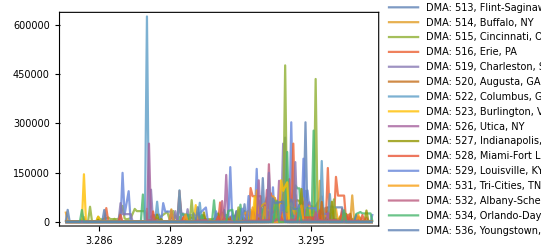

```mathematica
DateListPlot[
Transpose[rejectedcicada][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[rejectedcicada][[1]])]
```

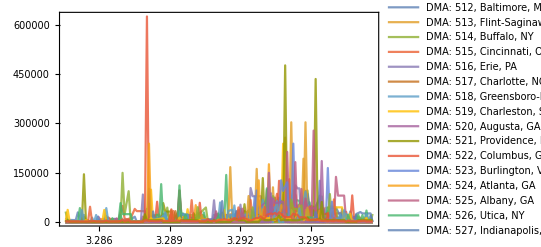

```mathematica
DateListPlot[
Transpose[cicadadata2][[2]]
,PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("DMA: "<>ToString[#]<>", "<>(#/.dmadict)[[2]]&/@Transpose[cicadadata2][[1]])]
```

```mathematica
cicadadata2[[1]][[2]]
```

{{Sun 1 Feb 2004,11834.3},{Mon 2 Feb 2004,5784.98},{Tue 3 Feb 2004,5784.98},{Wed 4 Feb 2004,5784.98},{Thu 5 Feb 2004,5544.95},{Fri 6 Feb 2004,5892.75},{Sat 7 Feb 2004,29069.8},{Sun 8 Feb 2004,5513.17},{Mon 9 Feb 2004,5513.17},{Tue 10 Feb 2004,5513.17},{Wed 11 Feb 2004,0.},{Thu 12 Feb 2004,0.},{Fri 13 Feb 2004,0.},{Sat 14 Feb 2004,0.},{Sun 15 Feb 2004,0.},{Mon 16 Feb 2004,0.},{Tue 17 Feb 2004,0.},{Wed 18 Feb 2004,0.},{Thu 19 Feb 2004,0.},{Fri 20 Feb 2004,6180.03},{Sat 21 Feb 2004,9680.54},{Sun 22 Feb 2004,11655.},{Mon 23 Feb 2004,5773.67},{Tue 24 Feb 2004,5773.67},{Wed 25 Feb 2004,0.},{Thu 26 Feb 2004,0.},{Fri 27 Feb 2004,0.},{Sat 28 Feb 2004,0.},{Sun 29 Feb 2004,0.},{Mon 1 Mar 2004,7041.83},{Tue 2 Mar 2004,7089.96},{Wed 3 Mar 2004,7138.1},{Thu 4 Mar 2004,7186.24},{Fri 5 Mar 2004,11529.6},{Sat 6 Mar 2004,15873.},{Sun 7 Mar 2004,0.},{Mon 8 Mar 2004,0.},{Tue 9 Mar 2004,0.},{Wed 10 Mar 2004,0.},{Thu 11 Mar 2004,0.},{Fri 12 Mar 2004,0.},{Sat 13 Mar 2004,0.},{Sun 14 Mar 2004,0.},{Mon 15 Mar 2004,5592.07},{Tue 16 Mar 2004,5719.08},{Wed 17 Mar 2004,5846.08},{Thu 18 Mar 2004,5973.09},{Fri 19 Mar 2004,6097.41},{Sat 20 Mar 2004,11862.4},{Sun 21 Mar 2004,11111.1},{Mon 22 Mar 2004,6862.73},{Tue 23 Mar 2004,6862.73},{Wed 24 Mar 2004,6862.73},{Thu 25 Mar 2004,9336.15},{Fri 26 Mar 2004,11809.6},{Sat 27 Mar 2004,17981.},{Sun 28 Mar 2004,24152.5},{Mon 29 Mar 2004,5103.34},{Tue 30 Mar 2004,10112.8},{Wed 31 Mar 2004,5029.46},{Thu 1 Apr 2004,5029.46},{Fri 2 Apr 2004,5120.87},{Sat 3 Apr 2004,5212.28},{Sun 4 Apr 2004,5303.68},{Mon 5 Apr 2004,5395.09},{Tue 6 Apr 2004,5486.5},{Wed 7 Apr 2004,8625.06},{Thu 8 Apr 2004,11574.1},{Fri 9 Apr 2004,7540.93},{Sat 10 Apr 2004,6260.32},{Sun 11 Apr 2004,6260.32},{Mon 12 Apr 2004,6260.32},{Tue 13 Apr 2004,6260.32},{Wed 14 Apr 2004,6260.32},{Thu 15 Apr 2004,15887.4},{Fri 16 Apr 2004,8789.86},{Sat 17 Apr 2004,11771.4},{Sun 18 Apr 2004,16229.6},{Mon 19 Apr 2004,12276.9},{Tue 20 Apr 2004,20965.},{Wed 21 Apr 2004,17388.7},{Thu 22 Apr 2004,15785.2},{Fri 23 Apr 2004,17217.5},{Sat 24 Apr 2004,11641.4},{Sun 25 Apr 2004,8031.9},{Mon 26 Apr 2004,8031.9},{Tue 27 Apr 2004,4940.21},{Wed 28 Apr 2004,16775.8},{Thu 29 Apr 2004,16170.5},{Fri 30 Apr 2004,13261.6},{Sat 1 May 2004,21055.5},{Sun 2 May 2004,30000.},{Mon 3 May 2004,18833.1},{Tue 4 May 2004,17793.2},{Wed 5 May 2004,11539.4},{Thu 6 May 2004,19180.},{Fri 7 May 2004,21174.6},{Sat 8 May 2004,21168.},{Sun 9 May 2004,29607.4},{Mon 10 May 2004,28134.1}}

```mathematica
cicadacone=Table[GeoPosition[Join[{#[[3]],#[[4]]}&[cicadadata2[[i]][[1]]/.dmadict],{τsimple[Transpose[{datetoindex[DateObject["feb-01-2004"],#]&/@#[[1]],#[[2]]}&[Transpose[cicadadata2[[i]][[2]]]]]]}]],{i,1,Length[cicadadata2]}];
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Part::pkspec1: The expression Transpose[{}] cannot be used as a part specification.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::pkspec1: The expression Transpose[{}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
GeoRegionValuePlot[Table[cicadacone[[i]]->Mod[i,2],{i,1,Length[cicadacone]}],GeoLabels->(Tooltip[#1,ToString[#2[[1]][[;;2]]/.latlongdict]<>" occured at "<> ToString@#2[[1]][[3]]]&),ColorFunction->ColorData["DarkRainbow"],GeoBackground->GeoStyling["ReliefMap"]]
```

LatitudeLongitude::invloc: GeoPosition[{{35.5708,-88.5302,(42 (101010.-List)+100 (102041.-List)+57 (111111.-List)+48 (114943.-List))/(429105.-4 List)}}] is not a valid location specification.

-Graphics-

```mathematica
ListPlot3D[Table[GeoGridPosition[cicadacone[[i]],"Mercator"][[1]],{i,1,Length[cicadacone]}],Mesh->All,PlotRange->All,AxesLabel->{"Latitude","Longitude","Time"}]
```

GeoGridPosition::invpos: GeoPosition[{35.5708,-88.5302,(42 (101010.-List)+100 (102041.-List)+57 (111111.-List)+48 (114943.-List))/(429105.-4 List)}] is not a valid position specification.

ListPlot3D::arrayerr: {{-76.5065,42.3801,96.8461},{-80.7695,37.989,106.661},{-80.4077,38.6266,107.441},{-71.3513,45.8533,111.621},«19»,{-71.4605,47.0387,103.501},{-79.659,44.248,91.6529},{-81.7112,45.1538,97.0031},{-77.9044,42.5799,99.3703}} must be a valid array or a list of valid arrays.

ListPlot3D[{{-76.5065,42.3801,96.8461},{-80.7695,37.989,106.661},{-80.4077,38.6266,107.441},{-71.3513,45.8533,111.621},{-84.3335,36.1014,110.927},{-83.6757,32.008,109.301},{-72.6594,45.8422,86.2057},{-82.7342,43.6749,112.683},{-81.8974,29.1848,88.0419},{-84.3548,43.8934,116.997},{-76.3721,39.388,92.1472},{-76.1014,47.6977,89.4801},{-77.535,40.4658,87.9028},{-78.4213,38.2908,110.668},{-76.882,44.0825,108.},{-78.4611,41.3667,106.887},{-87.8456,45.8454,99.0738},{-90.1693,41.6904,105.549},{-92.547,40.0393,95.6716},GeoPosition[{35.5708,-88.5302,(42 (101010.-List)+100 (102041.-List)+57 (111111.-List)+48 (114943.-List))/(429105.-4 List)}],{-86.6311,38.7229,95.3524},{-73.6073,44.8145,98.765},{-75.3875,43.5805,107.953},{-71.4605,47.0387,103.501},{-79.659,44.248,91.6529},{-81.7112,45.1538,97.0031},{-77.9044,42.5799,99.3703}},Mesh→All,PlotRange→All,AxesLabel→{Latitude,Longitude,Time}]

### Herpes Search Data from 2005 to 2015, USA, 1 day resolution.

Reasoning: STD’s are an obvious choice for this kind of analysis. They are well tracked, and spread person to person. They also prompt people to search for symptoms/medicines via Google. Unlike the Flu STDs are not seasonal and have (I would guess) I slower propagation rate and larger μ, which provides a different sort of test case. Other options are HIV, etc.
Difficulties: Same as the Flu; no clear origin/source.
Top Correlated Searches: HSV, Herpes Symptoms, Herpes Simplex, Herpes Genital

```mathematica
herpesdata=Import["~/Desktop/BioPhys/flu_project/data_inputs/herpes_data_2005-01-01_2015-01-01_day_2017-02-1006:07:15.342166.csv"];
For[i=2,i≤Length[herpesdata],i+=1,
herpesdata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[herpesdata[[i]][[4]],1],-1],","]];
];
```

```mathematica
Manipulate[
Module[{i,t},
t=tc;
Grid[{{DateObject["jan-01-2005"]+Quantity[1, "Days"]*(t-1)},
{GeoRegionValuePlot[Table[GeoPosition[{herpesdata[[i]][[2]],herpesdata[[i]][[3]]}]->herpesdata[[i]][[4]][[t]],{i,2,Length[herpesdata]}],ColorFunction->ColorData["TemperatureMap"]]}}]]
,Row[{Control[{tc,1,Length[cicadadata[[4]][[4]]],1}],Spacer[5],"t is in days",Spacer[2]}]]
```

GeoRegionValuePlot::reps: {} is not a list of rules of the form loc -> val

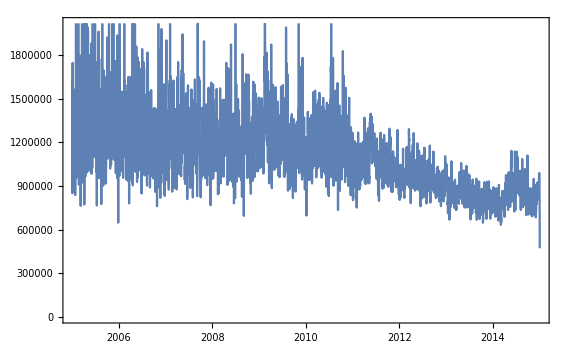

Part::partw: Part 15 of {{519,{{Thu 18 Jun 2009,9288.96},{Fri 19 Jun 2009,9193.76},{Sat 20 Jun 2009,9193.76},{Sun 21 Jun 2009,9193.76},{Mon 22 Jun 2009,9193.76},«41»,{Mon 3 Aug 2009,9043.54},{Tue 4 Aug 2009,8880.77},{Wed 5 Aug 2009,9050.82},{Thu 6 Aug 2009,9220.88},«256»}},«12»,{550,{{«1»},«49»,«256»}}} does not exist.

StringJoin::string: String expected at position 2 in «1».

StringJoin::string: String expected at position 4 in «1».

StringJoin::string: String expected at position 5 in «1».

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

DateListPlot::ldata: 15 is not a valid dataset or list of datasets.

```mathematica
DateListPlot[Table[{(DateObject["jan-01-2005"]+Quantity[1, "Days"]*(t-1))[[1]],Total@Table[herpesdata[[i]][[4]][[t]],{i,2,Length[herpesdata]}]},{t,1,Length[herpesdata[[2]][[4]]]}]]
```

```mathematica
Length[counties]
```

3143